```mathematica
ClearAll["Global`*"]
```

```mathematica
v=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/2d/square/polygon/solution/vertices.csv"];
v=Table[v[[i]],{i,2,Length[v]}]
```

```mathematica
dummy=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/2d/square/polygon/solution/edges.csv"]
```

```mathematica
i=18
dummy[[i,3]]
```

18

6

```mathematica
For[t={};i=2,i<=Length[dummy],i++,
If[dummy[[i,3]]==6,
AppendTo[t,{{v[[dummy[[i,1]]]][[1]],v[[dummy[[i,1]]]][[2]]},{v[[dummy[[i,2]]]][[1]],v[[dummy[[i,2]]]][[2]]}}]
]
]
```

```mathematica
t
```

{{{18,0.516639},{19,0.528512}},{{5,0.5},{6,0.454197}},{{6,0.454197},{7,0.417187}},{{8,0.401512},{9,0.399943}},{{12,0.322522},{13,0.281848}},{{16,0.379152},{17,0.460291}},{{9,0.399943},{10,0.393301}},{{11,0.366651},{12,0.322522}},{{13,0.281848},{14,0.271545}},{{17,0.460291},{18,0.516639}},{{15,0.306699},{16,0.379152}},{{5,0.5},{19,0.528512}},{{14,0.271545},{15,0.306699}},{{7,0.417187},{8,0.401512}},{{10,0.393301},{11,0.366651}}}

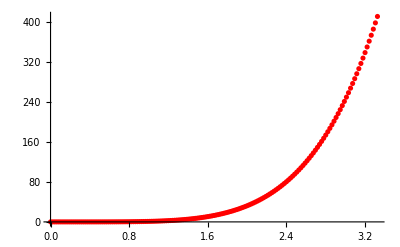

```mathematica
plotu1=ListPlot[t1,PlotStyle->Red]
```

```mathematica
Solve[{3π/2 a + b ==π+π/4,-3 π/2(1-a)+b==-π/4},{a,b}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b→(5 π)/4-(3 a π)/2}}

```mathematica
plotu1on0=ParametricPlot3D[{c[[1]]+R Cos[-3π/2 t+5π/4],c[[2]]+R Sin[-3π/2 t+5π/4],u1[3π /2 R t]},{t,0,1},PlotStyle->Blue,AspectRatio->Full]
```

-Graphics3D-

```mathematica
(*read u_0*)
```

```mathematica
t0=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/two_domains/solution/u_0_test.csv"]
t0=Table[{t0[[i,5]],t0[[i,6]],t0[[i,4]]},{i,2,Length[t0]}]
```

```mathematica
plotu0=ListPointPlot3D[t0,PlotStyle->{Green,PointSize->0.01}]
```

-Graphics3D-

```mathematica
Show[plotu0,plotu1on0,PlotRange->Full]
```

-Graphics3D-